```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
vPrior[θ_,α_,β_]:= PDF[BetaDistribution[α,β],θ]
vLikelihood[θ_,nSampleSize_Integer,nDiseased_Integer]:=Likelihood[BinomialDistribution[nSampleSize,θ],{nDiseased}]
vPosterior[θ_,nSampleSize_Integer,nDiseased_Integer,α_,β_]:= PDF[BetaDistribution[α+nDiseased,β + nSampleSize-nDiseased],θ]
fShowPriorLikelihoodPosterior[α_,β_,nSampleSize_Integer,nDiseased_Integer]:=Module[{},Show[GraphicsColumn[{Plot[vPrior[θ,α,β],{θ,0,1},Frame->{True,True,False,False},FrameTicks->{True,False},FrameLabel->{"θ","pdf"},PlotLabel->"prior",PlotStyle->Blue,PlotRange->Full],Plot[vLikelihood[θ,nSampleSize,nDiseased],{θ,0,1},Frame->{True,True,False,False},FrameTicks->{True,False},PlotRange->Full,FrameLabel->{"θ","likelihood"},PlotStyle->Blue,PlotLabel->"likelihood"],Plot[vPosterior[θ,nSampleSize,nDiseased,α,β],{θ,0,1},Frame->{True,True,False,False},FrameTicks->{True,False},PlotRange->Full,FrameLabel->{"θ","pdf"},PlotStyle->Blue,PlotLabel->"posterior"]}],ImageSize->400]]
```

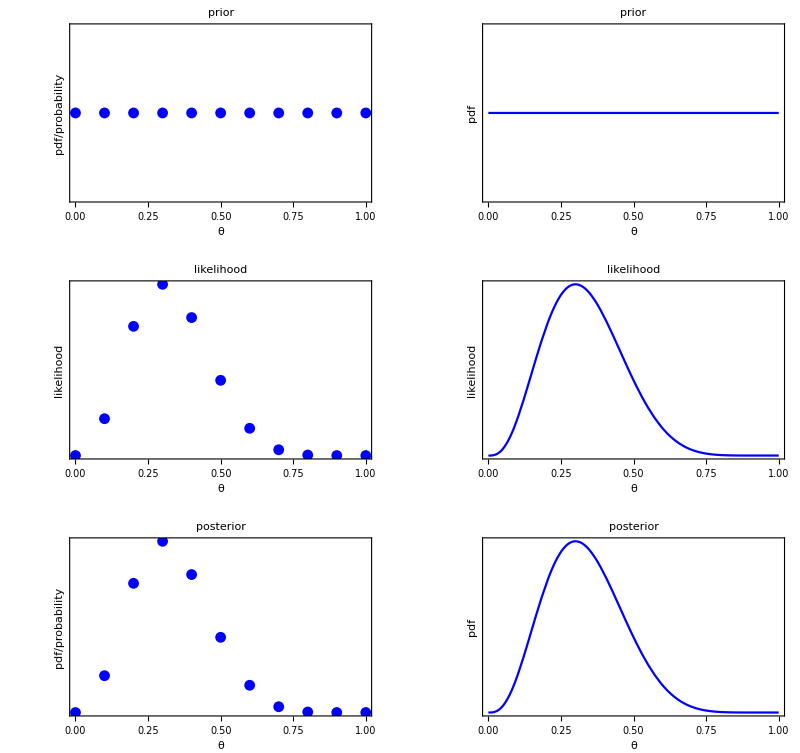

```mathematica
g1D=ListPlot[Join[{{0,1},{1,1}},Table[{θ,vPrior[θ,1,1]},{θ,0.1,0.9,0.1}]],Frame->{True,True,False,False},FrameTicks->{True,False},FrameLabel->{"θ","pdf/probability"},PlotLabel->"prior",PlotStyle->Blue,PlotRange->Full];
g2D=ListPlot[Table[{θ,vLikelihood[θ,10,3]},{θ,0,1,0.1}],Frame->{True,True,False,False},FrameTicks->{True,False},FrameLabel->{"θ","likelihood"},PlotLabel->"likelihood",PlotStyle->Blue,PlotRange->Full];
g3D=ListPlot[Table[{θ,vPosterior[θ,10,3,1,1]},{θ,0,1,0.1}],Frame->{True,True,False,False},FrameTicks->{True,False},FrameLabel->{"θ","pdf/probability"},PlotLabel->"posterior",PlotStyle->Blue,PlotRange->Full];
g1=Plot[vPrior[θ,1,1],{θ,0,1},Frame->{True,True,False,False},FrameTicks->{True,False},FrameLabel->{"θ","pdf"},PlotLabel->"prior",PlotStyle->Blue,PlotRange->Full];
g2=Plot[vLikelihood[θ,10,3],{θ,0,1},Frame->{True,True,False,False},FrameTicks->{True,False},PlotRange->Full,FrameLabel->{"θ","likelihood"},PlotStyle->Blue,PlotLabel->"likelihood"];
g3=Plot[vPosterior[θ,10,3,1,1],{θ,0,1},Frame->{True,True,False,False},FrameTicks->{True,False},PlotRange->Full,FrameLabel->{"θ","pdf"},PlotStyle->Blue,PlotLabel->"posterior"];
gFinal=Show[GraphicsGrid[{{g1D,g1},{g2D,g2},{g3D,g3}}],ImageSize->800]
```

```mathematica
Export["Prior_diseaseDiscretised.pdf",gFinal]
```

Prior_diseaseDiscretised.pdf